```mathematica
F-H实验数据处理
```

F-H实验数据处理

```mathematica
1.数据导入
```

1. 数据导入

```mathematica
Clear[data,datalowpoints];
(*数据比较多，建议先写在excel中再导入mathematica*)
data=Import["documents/dataofFH.xlsx"][[1,All,All]]
(*极值点数据靠自己看表输入*)
datalowpoints={{21.75,0.050},{32,0.045},{42.75,0.044},{53.5,0.052},{65,0.072},{77,0.101},{89.25,0.143}}
```

{{10.,0.037},{12.,0.042},{14.,0.055},{15.,0.061},{15.5,0.063},{16.,0.065},{16.5,0.066},{17.,0.067},{17.5,0.067},{18.,0.066},{18.5,0.065},{19.,0.063},{19.5,0.061},{20.,0.059},{20.5,0.056},{21.,0.053},{21.5,0.05},{22.,0.05},{22.5,0.053},{23.,0.059},{23.5,0.067},{24.5,0.076},{25.5,0.097},{26.,0.1},{26.5,0.104},{27.,0.104},{27.5,0.102},{28.,0.098},{28.5,0.093},{29.5,0.079},{30.5,0.06},{31.,0.054},{31.5,0.048},{32.,0.045},{32.5,0.046},{33.,0.056},{33.5,0.069},{34.5,0.089},{35.5,0.119},{36.5,0.137},{37.,0.138},{37.5,0.138},{38.,0.134},{38.5,0.127},{39.,0.119},{40.,0.093},{40.5,0.082},{41.,0.069},{42.,0.05},{42.5,0.044},{43.,0.044},{43.5,0.051},{44.,0.065},{45.,0.086},{46.,0.125},{46.5,0.141},{47.,0.149},{47.5,0.154},{48.,0.159},{48.5,0.159},{49.,0.156},{49.5,0.149},{50.5,0.129},{51.5,0.099},{52.5,0.071},{53.,0.059},{53.5,0.052},{54.,0.054},{54.5,0.063},{55.,0.077},{56.,0.098},{57.,0.134},{58.,0.163},{58.5,0.171},{59.,0.175},{59.5,0.178},{60.,0.178},{60.5,0.174},{61.,0.167},{62.,0.146},{63.,0.118},{64.,0.087},{64.5,0.078},{65.,0.072},{65.5,0.074},{66.,0.082},{68.,0.136},{69.,0.153},{70.,0.179},{70.5,0.186},{71.,0.191},{71.5,0.194},{72.,0.192},{72.5,0.189},{73.,0.182},{75.,0.137},{76.,0.111},{76.5,0.104},{77.,0.101},{77.5,0.104},{78.,0.11},{80.,0.149},{82.,0.196},{83.,0.209},{83.5,0.211},{84.,0.211},{84.5,0.21},{85.,0.206},{86.,0.191},{88.,0.152},{89.,0.143},{89.5,0.143},{90.,0.146},{91.,0.159},{93.,0.199},{95.,0.23},{95.5,0.233},{96.,0.236}}

{{21.75,0.05},{32,0.045},{42.75,0.044},{53.5,0.052},{65,0.072},{77,0.101},{89.25,0.143}}

## 2. 数据处理

InterpolatingFunction[…]

InterpolatingFunction[…]

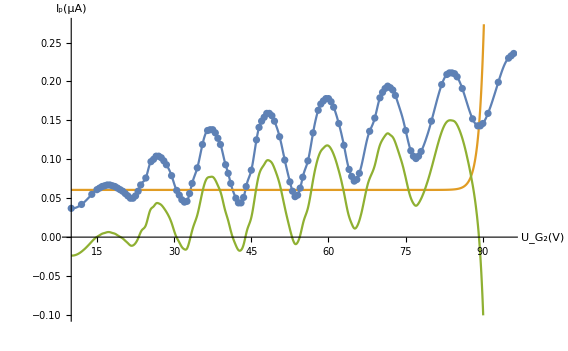

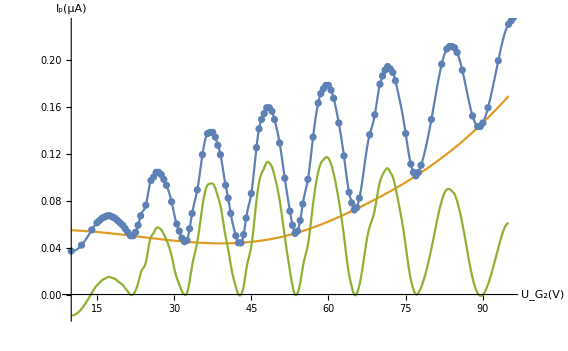

```mathematica
Clear[fi,model,a,b,c,d,e,x,lowf,lowfi];
fi=Interpolation[data,InterpolationOrder->3,Method->"Spline"]
(*这个是老师要求的指数拟合（十分不得行）*)
model=a Exp[e x]+c;
fitf=FindFit[datalowpoints,model,{a,b,c,d,e},x];
lowf[x_]:=model/.fitf;
(*这个是直接拿内插拟合的极值点曲线*)
lowfi=Interpolation[datalowpoints,InterpolationOrder->3,Method->"Spline"]
(*分别是两种拟合的图像*)
Show[Plot[{fi[x],lowf[x],fi[x]-lowf[x]},{x,10,95}],ListPlot[data],AxesLabel->{"U_G_2(V)","I_p(μA)"}]
Show[Plot[{fi[x],lowfi[x],fi[x]-lowfi[x]},{x,10,95}],ListPlot[data],AxesLabel->{"U_G_2(V)","I_p(μA)"}]
```